```mathematica
$Assumptions = K ∈ Reals && D ∈ Reals  && O ∈ Reals && K ≥ 0 && D ≥ 0 && O ≥ 0 && t ≥ 0 && tsep ≥ 0 && t≥tsep
```

K∈ℝ&&D∈ℝ&&O∈ℝ&&K≥0&&D≥0&&O≥0&&t≥0&&tsep≥0&&t≥tsep

```mathematica
M = {{0, O/2},{O/2, D}}
```

{{0,O/2},{O/2,D}}

```mathematica
F = {{0,0},{0,K}}
```

{{0,0},{0,K}}

```mathematica
expM[t_]:= FullSimplify[MatrixExp[-I *t *M]]
```

```mathematica
expM[t]
```

{{ⅇ^(-1/2 ⅈ D t) (Cos[1/2 √(D^2+O^2) t]+(ⅈ D Sin[1/2 √(D^2+O^2) t])/(√(D^2+O^2))),-(ⅈ ⅇ^(-1/2 ⅈ D t) O Sin[1/2 √(D^2+O^2) t])/(√(D^2+O^2))},{-(ⅈ ⅇ^(-1/2 ⅈ D t) O Sin[1/2 √(D^2+O^2) t])/(√(D^2+O^2)),ⅇ^(-1/2 ⅈ D t) (Cos[1/2 √(D^2+O^2) t]-(ⅈ D Sin[1/2 √(D^2+O^2) t])/(√(D^2+O^2)))}}

```mathematica
expF = FullSimplify[MatrixExp[-I*F]]
```

{{1,0},{0,ⅇ^(-ⅈ K)}}

```mathematica
U [t_, tsep_]:= FullSimplify[expM[t].expF.expM[tsep].expF]
```

```mathematica
U[t, tsep]  //MatrixForm
```

$Aborted

```mathematica
Uavr[tsep_]:=FullSimplify[Expectation[Uavr[t, tsep],Distributed[t,UniformDistribution[{0,4π/√(D^2+O^2)}]]]]
```

```mathematica
Rho0 = {{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
Rho[t_,tsep_] := FullSimplify[U[t,tsep].Rho0.ConjugateTranspose[U[t,tsep]]]
```

```mathematica
RhoR[t_] := FullSimplify[Expectation[expM[t].Rho0.ConjugateTranspose[expM[t]],Distributed[t,UniformDistribution[{0,4π/√(D^2+O^2)}]]], D > 0 && O>0]
```

```mathematica
Rho11 = FullSimplify[1/(2 (D^2+O^2))ⅇ^(-1/2 ⅈ (2 K+D (t+tsep))) ((-1+ⅇ^(ⅈ K)) O^2 Cos[1/2 √(D^2+O^2) (t-tsep)]+(O^2+ⅇ^(ⅈ K) (2 D^2+O^2)) Cos[1/2 √(D^2+O^2) (t+tsep)]+2 ⅈ D ⅇ^(ⅈ K) √(D^2+O^2) Sin[1/2 √(D^2+O^2) (t+tsep)])*Conjugate[1/(2 (D^2+O^2))ⅇ^(-1/2 ⅈ (2 K+D (t+tsep))) ((-1+ⅇ^(ⅈ K)) O^2 Cos[1/2 √(D^2+O^2) (t-tsep)]+(O^2+ⅇ^(ⅈ K) (2 D^2+O^2)) Cos[1/2 √(D^2+O^2) (t+tsep)]+2 ⅈ D ⅇ^(ⅈ K) √(D^2+O^2) Sin[1/2 √(D^2+O^2) (t+tsep)])]]
```

1/(4 (D^2+O^2)^2)Conjugate[(-1+ⅇ^(ⅈ K)) O^2 Cos[1/2 √(D^2+O^2) (t-tsep)]+(O^2+ⅇ^(ⅈ K) (2 D^2+O^2)) Cos[1/2 √(D^2+O^2) (t+tsep)]+2 ⅈ D ⅇ^(ⅈ K) √(D^2+O^2) Sin[1/2 √(D^2+O^2) (t+tsep)]] ((-1+ⅇ^(ⅈ K)) O^2 Cos[1/2 √(D^2+O^2) (t-tsep)]+(O^2+ⅇ^(ⅈ K) (2 D^2+O^2)) Cos[1/2 √(D^2+O^2) (t+tsep)]+2 ⅈ D ⅇ^(ⅈ K) √(D^2+O^2) Sin[1/2 √(D^2+O^2) (t+tsep)])

```mathematica
RhoR[t] //MatrixForm
```

(1/2 (1+D^2/(D^2+O^2)) | -(D O)/(2 (D^2+O^2))
-(D O)/(2 (D^2+O^2)) | O^2/(2 (D^2+O^2)))

```mathematica
TableForm[{{1/2 (1+D^2/(D^2+O^2)),-(D O)/(2 (D^2+O^2))},{-(D O)/(2 (D^2+O^2)),O^2/(2 (D^2+O^2))}}]
```

1/2 (1+D^2/(D^2+O^2)) | -(D O)/(2 (D^2+O^2))
-(D O)/(2 (D^2+O^2)) | O^2/(2 (D^2+O^2))

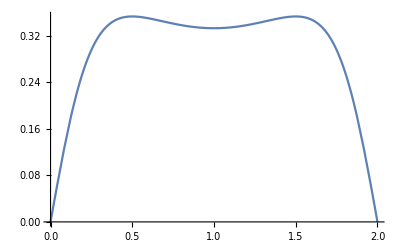

```mathematica
Plot[Abs[Sin[x/2*π]/(2-Cos[x*π])],{x, 0 , 2}]
```

```mathematica
FullSimplify[(2 D^2+O^2-D (D (Cos[K]-(-1+Cos[K]) Cos[√(D^2+O^2) tsep])+√(D^2+O^2) Sin[K] Sin[√(D^2+O^2) tsep]))/(2 (D^2+O^2)^2)+Sin[K/2]Sin[K/2+tsep], O==0 && D==1]
```

1-Cos[K]/2

```mathematica
Rh0T = {{1/2 (1+D/(√(D^2+O^2))),-O/(2 √(D^2+O^2))},{-O/(2 √(D^2+O^2)),1/2-D/(2 √(D^2+O^2))}}
```

{{1/2 (1+D/(√(D^2+O^2))),-O/(2 √(D^2+O^2))},{-O/(2 √(D^2+O^2)),1/2-D/(2 √(D^2+O^2))}}

```mathematica
FullSimplify[expM[t].Rh0T.ConjugateTranspose[expM[t]]]
```

{{1/2 (1+D/(√(D^2+O^2))),-O/(2 √(D^2+O^2))},{-O/(2 √(D^2+O^2)),1/2-D/(2 √(D^2+O^2))}}